### Categorization

Tutorial

Indivaria

Indivaria`

Indivaria/tutorial/18

### Keywords

Details

# Model 1.8

Model 1.8 is the model for estimating the number of sequestered parasites in a patient during treatment with antimalarial drug. It was proposed by Gravenor M. B, et al., (1998, Estimating sequestered parasite population dynamics in cerebral malaria Proceedings of the National Academy of Sciences of the United States of America 95, 7620-7624). The parasites are divided into two group: circulating (n1) and sequestered (n2). The relation between these two group is as shown below and can be writtein as

-Graphics-

-Graphics-

The output of model 1.8 is the list of n1 and n2 from solving above equations.

model | model ID
initn | the initial number of n1 and n2 #{ n1(o), n2(0) }
lambdals | the maturation rate (λ1) and the invasion rate λ2 # {λ1, λ2}
r | the parasite multiplication rate (R)
muls | the death rate # {μ1, μ2}
runmax | the number of run time of the model (hours)
stepsize | the step size of the model output
outform | the output format; model 1.8 has only one output form (0)

The list of parasmeters for model 1.8.

Example of the results from model 1.8

```mathematica
lsout=IDVL["mod1_8.in"];
```

******INDIVARIA*****

model: 1.8

outform: 0

********************

model: 1.8

initn: {1000,200}

lambdals: {0.0309,0.0438}

muls: {0.1,0.25}

r: 8.3

runsteps: 60

stepsize: 0.1

outform: 0

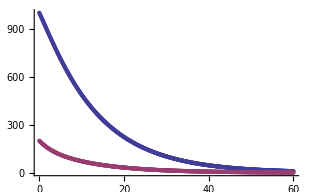

```mathematica
ListPlot[{lsout[[All,{1,2}]],lsout[[All,{1,3}]]},PlotRange->All]
```

More About

List of models

Related Tutorials

Using Indivaria

Related Wolfram Education Group Courses